```mathematica
Solve[vf k+cq vf k k ==μ,k]
```

{{k→(-vf-√vf √(vf+4 cq μ))/(2 cq vf)},{k→(-vf+√vf √(vf+4 cq μ))/(2 cq vf)}}

## sigma

```mathematica
Clear[sig,B,tra11,β00,ter11,β10,vomm1,vomm2,vdotk1,vdotk2,kf1,kf2,h10,h20,h11,h21];

sig[B_,μ_,vf_,cq_,tra11_,ter11_]:=Block[{e=1,vvec11,vvec21,θ,ϕ=0,θp,chi,Dphase1,Dphase2,vomm11,vomm21,vdotk11,vdotk21,colvec,mat,sol,Λ11,Λ21,a11,b11,c11,a21,b21,c21,conteq,matr,totmat,kf11,kf21,h11,h21,τ11,τ21,f11,f21,ct411,st411,ct4ct411,st4st411,ct4st411,ct4st211,st211,st4st211,st2st211,ct421,st421,ct4ct421,st4st421,ct4st221,st221,st4st221,st2st221,ct4st421,hct411, hct421,hst411,hst421,hst211,hst221,zero11,zero21,hzero21,hzero11,conteq1,int11,int21,s11,s21},

chi=1;
(******** first node ***************)
kf11[θ_]=(-vf+√vf √(vf+4 cq μ))/(2 cq vf);

vvec11[θ_]=vf(1+2cq kf11[θ]){ Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]};
vomm11[θ_]={0,0,0};

Dphase1[θ_]=1-(B e Cos[θ])/kf11[θ]^2;
vdotk11[θ_]=vf kf11[θ] (1+2 cq kf11[θ]);
h11[θ_]=1/Dphase1[θ]((1+2 cq kf11[θ]) vf Cos[θ]+e B chi vf(-2 kf11[θ]^2 (1+2 cq kf11[θ]))/(2 kf11[θ]^4));
(******** second node ***************)
chi=-1;

kf21[θ_]=(-vf+√vf √(vf+4 cq μ))/(2 cq vf);
vvec21[θ_]=vf(1+2cq kf21[θ]){ Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]};
vomm21[θ_]={0,0,0};

Dphase2[θ_]=1+(B e Cos[θ])/kf21[θ]^2;
vdotk21[θ_]=vf kf21[θ] (1+2 cq kf21[θ]);
h21[θ_]=1/Dphase2[θ]((1+2 cq kf21[θ]) vf Cos[θ]+e B chi vf(-2 kf21[θ]^2 (1+2 cq kf21[θ]))/(2 kf21[θ]^4));


(***************************************************************************************************************)
(* -Graphics- *)
τ11[θ_]=(tra11 Cos[θ/2]^4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Cos[θp/2]^4,{θp,0,π}]+
tra11 Sin[θ/2]^4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Sin[θp/2]^4,{θp,0,π}]+(tra11 Sin[θ]^2)/4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Sin[θp]^2,{θp,0,π}]+
(***** conjugate node  *****)
ter11 Sin[θ/2]^4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Cos[θp/2]^4,{θp,0,π}]+ter11 Cos[θ/2]^4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Sin[θp/2]^4,{θp,0,π}]+(ter11 Sin[θ]^2)/4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Sin[θp]^2,{θp,0,π}])^-1;
(********************************)
τ21[θ_]=(tra11 Cos[θ/2]^4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Cos[θp/2]^4,{θp,0,π}]+
tra11 Sin[θ/2]^4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Sin[θp/2]^4,{θp,0,π}]+(tra11 Sin[θ]^2)/4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Sin[θp]^2,{θp,0,π}]+
(***** conjugate node  *****)
ter11 Sin[θ/2]^4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Cos[θp/2]^4,{θp,0,π}]+ter11 Cos[θ/2]^4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Sin[θp/2]^4,{θp,0,π}]+(ter11 Sin[θ]^2)/4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Sin[θp]^2,{θp,0,π}])^-1;
(********************************)

(*-Graphics-*)
f11[θ_]=(Sin[θ] (kf11[θ])^3)/Abs[vdotk11[θ]] Dphase1[θ] τ11[θ];
f21[θ_]=(Sin[θ] (kf21[θ])^3)/Abs[vdotk21[θ]] Dphase2[θ]τ21[θ];

zero11=Quiet[NIntegrate [f11[θ],{θ,0,π}]];
st411=Quiet[NIntegrate [f11[θ] Sin[θ/2]^4,{θ,0,π}]];
ct411=Quiet[NIntegrate [f11[θ] Cos[θ/2]^4,{θ,0,π}]];
ct4st411=Quiet[NIntegrate [f11[θ] Cos[θ/2]^4 Sin[θ/2]^4,{θ,0,π}]];
ct4ct411=Quiet[NIntegrate [f11[θ] Cos[θ/2]^8,{θ,0,π}]];st4st411=Quiet[NIntegrate [f11[θ] Sin[θ/2]^8,{θ,0,π}]];
ct4st211=Quiet[NIntegrate [f11[θ] Cos[θ/2]^4 Sin[θ]^2,{θ,0,π}]];
st211=Quiet[NIntegrate [f11[θ] Sin[θ]^2,{θ,0,π}]];
st4st211=Quiet[NIntegrate [f11[θ] Sin[θ/2]^4 Sin[θ]^2,{θ,0,π}]];
st2st211=Quiet[NIntegrate [f11[θ] Sin[θ]^4,{θ,0,π}]];

zero21=Quiet[NIntegrate [f21[θ],{θ,0,π}]];ct421=Quiet[NIntegrate [f21[θ] Cos[θ/2]^4,{θ,0,π}]];st421=Quiet[NIntegrate [f21[θ] Sin[θ/2]^4,{θ,0,π}]];
ct4st421=Quiet[NIntegrate [f21[θ] Cos[θ/2]^4 Sin[θ/2]^4,{θ,0,π}]];
ct4ct421=Quiet[NIntegrate [f21[θ] Cos[θ/2]^8,{θ,0,π}]];st4st421=Quiet[NIntegrate [f21[θ] Sin[θ/2]^8,{θ,0,π}]];
ct4st221=Quiet[NIntegrate [f21[θ] Cos[θ/2]^4 Sin[θ]^2,{θ,0,π}]];
st221=Quiet[NIntegrate [f21[θ] Sin[θ]^2,{θ,0,π}]];
st4st221=Quiet[NIntegrate [f21[θ] Sin[θ/2]^4 Sin[θ]^2,{θ,0,π}]];
st2st221=Quiet[NIntegrate [f21[θ] Sin[θ]^4,{θ,0,π}]];

hzero11=Quiet[NIntegrate [f11[θ]h11[θ],{θ,0,π}]];
hct411=Quiet[NIntegrate [f11[θ]h11[θ] Cos[θ/2]^4,{θ,0,π}]];
hst411=Quiet[NIntegrate [f11[θ]h11[θ] Sin[θ/2]^4,{θ,0,π}]];
hst211=Quiet[NIntegrate [f11[θ]h11[θ] Sin[θ]^2,{θ,0,π}]];

hzero21=Quiet[NIntegrate [f21[θ]h21[θ],{θ,0,π}]];hct421=Quiet[NIntegrate [f21[θ]h21[θ] Cos[θ/2]^4,{θ,0,π}]];hst421=Quiet[NIntegrate [f21[θ]h21[θ] Sin[θ/2]^4,{θ,0,π}]];
hst221=Quiet[NIntegrate [f21[θ]h21[θ] Sin[θ]^2,{θ,0,π}]];


colvec=({{hst421 ter11+hct411 tra11}, {hct421 ter11+hst411 tra11}, {1/4 (hst221 ter11+hst211 tra11)}, {hst411 ter11+hct421 tra11}, {hct411 ter11+hst421 tra11}, {1/4 (hst211 ter11+hst221 tra11)}});
matr=({{1-ct4ct411 tra11, -ct4st411 tra11, -ct4st211 tra11, -ct4st421 ter11, -st4st421 ter11, -st4st221 ter11}, {-ct4st411 tra11, 1-st4st411 tra11, -st4st211 tra11, -ct4ct421 ter11, -ct4st421 ter11, -ct4st221 ter11}, {-(ct4st211 tra11)/4, -(st4st211 tra11)/4, 1-(st2st211 tra11)/4, -(ct4st221 ter11)/4, -(st4st221 ter11)/4, -(st2st221 ter11)/4}, {-ct4st411 ter11, -st4st411 ter11, -st4st211 ter11, 1-ct4ct421 tra11, -ct4st421 tra11, -ct4st221 tra11}, {-ct4ct411 ter11, -ct4st411 ter11, -ct4st211 ter11, -ct4st421 tra11, 1-st4st421 tra11, -st4st221 tra11}, {-(ct4st211 ter11)/4, -(st4st211 ter11)/4, -(st2st211 ter11)/4, -(ct4st221 tra11)/4, -(st4st221 tra11)/4, 1-(st2st221 tra11)/4}});
mat=matr.{a11,b11,c11,a21,b21,c21};

conteq=(a11 ct411-hzero11+c11 st211+b11 st411)+(a21 ct421-hzero21+c21 st221+b21 st421);

sol=Flatten[Solve[{mat[[1]]+colvec[[1]]==0,mat[[2]]+colvec[[2]]==0,mat[[3]]+colvec[[3]]==0,mat[[4]]+colvec[[4]]==0,mat[[5]]+colvec[[5]]==0,mat[[6]]+colvec[[6]]==0,conteq==0},{a11,b11,c11,a21,b21,c21}],1]//Chop;

Λ11[θ_]=τ11[θ](-h11[θ]+a11  Cos[θ/2]^4 +b11 Sin[θ/2]^4+c11 Sin[θ]^2)/.sol;
Λ21[θ_]=τ21[θ](-h21[θ]+a21 Cos[θ/2]^4+b21 Sin[θ/2]^4+c21 Sin[θ]^2)/.sol;

(* -Graphics- *)
int11[θ_]=-(Sin[θ] (kf11[θ])^3)/Abs[vdotk11[θ]]( e^2 B vf(-2 kf11[θ]^2 (1+ 2 cq kf11[θ]))/(2 kf11[θ]^4)+ e(vvec11[θ])[[3]])Λ11[θ];
int21[θ_]=-(Sin[θ] (kf21[θ])^3)/Abs[vdotk21[θ]](e^2 B vf(2 kf21[θ]^2 (1+2 cq kf21[θ]))/(2 kf21[θ]^4) + e(vvec21[θ])[[3]] )Λ21[θ];

s11=NIntegrate[int11[θ],{θ,0,π}]//Quiet;
s21=NIntegrate[int21[θ],{θ,0,π}]//Quiet;

{B,{s11,s21},s11+s21,MatrixRank[matr],MatrixForm[{a11,b11,c11,a21,b21,c21}/.sol]}
];
```

## sigma B=0

```mathematica
Clear[sig0,B,tra11,β00,ter11,β10,vomm1,vomm2,vdotk1,vdotk2,kf1,kf2,h10,h20,h11,h21];

sig0[μ_,vf_,cq_,tra11_,ter11_]:=Block[{B=0,e=1,vvec11,vvec21,θ,ϕ=0,θp,chi,Dphase1,Dphase2,vomm11,vomm21,vdotk11,vdotk21,colvec,mat,sol,Λ11,Λ21,a11,b11,c11,a21,b21,c21,conteq,matr,totmat,kf11,kf21,h11,h21,τ11,τ21,f11,f21,ct411,st411,ct4ct411,st4st411,ct4st411,ct4st211,st211,st4st211,st2st211,ct421,st421,ct4ct421,st4st421,ct4st221,st221,st4st221,st2st221,ct4st421,hct411, hct421,hst411,hst421,hst211,hst221,zero11,zero21,hzero21,hzero11,conteq1,int11,int21,s11,s21},

chi=1;
(******** first node ***************)
kf11[θ_]=(-vf+√vf √(vf+4 cq μ))/(2 cq vf);

vvec11[θ_]=vf(1+2cq kf11[θ]){ Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]};
vomm11[θ_]={0,0,0};

Dphase1[θ_]=1;
vdotk11[θ_]=vf kf11[θ] (1+2 cq kf11[θ]);
h11[θ_]=1/Dphase1[θ]((1+2 cq kf11[θ]) vf Cos[θ]);
(******** second node ***************)
chi=-1;

kf21[θ_]=(-vf+√vf √(vf+4 cq μ))/(2 cq vf);
vvec21[θ_]=vf(1+2cq kf21[θ]){ Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]};
vomm21[θ_]={0,0,0};

Dphase2[θ_]=1;
vdotk21[θ_]=vf kf21[θ] (1+2 cq kf21[θ]);
h21[θ_]=1/Dphase2[θ]((1+2 cq kf21[θ]) vf Cos[θ]);


(***************************************************************************************************************)
(* -Graphics- *)
τ11[θ_]=(tra11 Cos[θ/2]^4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Cos[θp/2]^4,{θp,0,π}]+
tra11 Sin[θ/2]^4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Sin[θp/2]^4,{θp,0,π}]+(tra11 Sin[θ]^2)/4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Sin[θp]^2,{θp,0,π}]+
(***** conjugate node  *****)
ter11 Sin[θ/2]^4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Cos[θp/2]^4,{θp,0,π}]+ter11 Cos[θ/2]^4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Sin[θp/2]^4,{θp,0,π}]+(ter11 Sin[θ]^2)/4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Sin[θp]^2,{θp,0,π}])^-1;
(********************************)
τ21[θ_]=(tra11 Cos[θ/2]^4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Cos[θp/2]^4,{θp,0,π}]+
tra11 Sin[θ/2]^4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Sin[θp/2]^4,{θp,0,π}]+(tra11 Sin[θ]^2)/4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Sin[θp]^2,{θp,0,π}]+
(***** conjugate node  *****)
ter11 Sin[θ/2]^4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Cos[θp/2]^4,{θp,0,π}]+ter11 Cos[θ/2]^4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Sin[θp/2]^4,{θp,0,π}]+(ter11 Sin[θ]^2)/4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Sin[θp]^2,{θp,0,π}])^-1;
(********************************)

(*-Graphics-*)
f11[θ_]=(Sin[θ] (kf11[θ])^3)/Abs[vdotk11[θ]] Dphase1[θ] τ11[θ];
f21[θ_]=(Sin[θ] (kf21[θ])^3)/Abs[vdotk21[θ]] Dphase2[θ]τ21[θ];

zero11=Quiet[NIntegrate [f11[θ],{θ,0,π}]];
st411=Quiet[NIntegrate [f11[θ] Sin[θ/2]^4,{θ,0,π}]];
ct411=Quiet[NIntegrate [f11[θ] Cos[θ/2]^4,{θ,0,π}]];
ct4st411=Quiet[NIntegrate [f11[θ] Cos[θ/2]^4 Sin[θ/2]^4,{θ,0,π}]];
ct4ct411=Quiet[NIntegrate [f11[θ] Cos[θ/2]^8,{θ,0,π}]];st4st411=Quiet[NIntegrate [f11[θ] Sin[θ/2]^8,{θ,0,π}]];
ct4st211=Quiet[NIntegrate [f11[θ] Cos[θ/2]^4 Sin[θ]^2,{θ,0,π}]];
st211=Quiet[NIntegrate [f11[θ] Sin[θ]^2,{θ,0,π}]];
st4st211=Quiet[NIntegrate [f11[θ] Sin[θ/2]^4 Sin[θ]^2,{θ,0,π}]];
st2st211=Quiet[NIntegrate [f11[θ] Sin[θ]^4,{θ,0,π}]];

zero21=Quiet[NIntegrate [f21[θ],{θ,0,π}]];ct421=Quiet[NIntegrate [f21[θ] Cos[θ/2]^4,{θ,0,π}]];st421=Quiet[NIntegrate [f21[θ] Sin[θ/2]^4,{θ,0,π}]];
ct4st421=Quiet[NIntegrate [f21[θ] Cos[θ/2]^4 Sin[θ/2]^4,{θ,0,π}]];
ct4ct421=Quiet[NIntegrate [f21[θ] Cos[θ/2]^8,{θ,0,π}]];st4st421=Quiet[NIntegrate [f21[θ] Sin[θ/2]^8,{θ,0,π}]];
ct4st221=Quiet[NIntegrate [f21[θ] Cos[θ/2]^4 Sin[θ]^2,{θ,0,π}]];
st221=Quiet[NIntegrate [f21[θ] Sin[θ]^2,{θ,0,π}]];
st4st221=Quiet[NIntegrate [f21[θ] Sin[θ/2]^4 Sin[θ]^2,{θ,0,π}]];
st2st221=Quiet[NIntegrate [f21[θ] Sin[θ]^4,{θ,0,π}]];

hzero11=Quiet[NIntegrate [f11[θ]h11[θ],{θ,0,π}]];
hct411=Quiet[NIntegrate [f11[θ]h11[θ] Cos[θ/2]^4,{θ,0,π}]];
hst411=Quiet[NIntegrate [f11[θ]h11[θ] Sin[θ/2]^4,{θ,0,π}]];
hst211=Quiet[NIntegrate [f11[θ]h11[θ] Sin[θ]^2,{θ,0,π}]];

hzero21=Quiet[NIntegrate [f21[θ]h21[θ],{θ,0,π}]];hct421=Quiet[NIntegrate [f21[θ]h21[θ] Cos[θ/2]^4,{θ,0,π}]];hst421=Quiet[NIntegrate [f21[θ]h21[θ] Sin[θ/2]^4,{θ,0,π}]];
hst221=Quiet[NIntegrate [f21[θ]h21[θ] Sin[θ]^2,{θ,0,π}]];


colvec=({{hst421 ter11+hct411 tra11}, {hct421 ter11+hst411 tra11}, {1/4 (hst221 ter11+hst211 tra11)}, {hst411 ter11+hct421 tra11}, {hct411 ter11+hst421 tra11}, {1/4 (hst211 ter11+hst221 tra11)}});
matr=({{1-ct4ct411 tra11, -ct4st411 tra11, -ct4st211 tra11, -ct4st421 ter11, -st4st421 ter11, -st4st221 ter11}, {-ct4st411 tra11, 1-st4st411 tra11, -st4st211 tra11, -ct4ct421 ter11, -ct4st421 ter11, -ct4st221 ter11}, {-(ct4st211 tra11)/4, -(st4st211 tra11)/4, 1-(st2st211 tra11)/4, -(ct4st221 ter11)/4, -(st4st221 ter11)/4, -(st2st221 ter11)/4}, {-ct4st411 ter11, -st4st411 ter11, -st4st211 ter11, 1-ct4ct421 tra11, -ct4st421 tra11, -ct4st221 tra11}, {-ct4ct411 ter11, -ct4st411 ter11, -ct4st211 ter11, -ct4st421 tra11, 1-st4st421 tra11, -st4st221 tra11}, {-(ct4st211 ter11)/4, -(st4st211 ter11)/4, -(st2st211 ter11)/4, -(ct4st221 tra11)/4, -(st4st221 tra11)/4, 1-(st2st221 tra11)/4}});
mat=matr.{a11,b11,c11,a21,b21,c21};

conteq=(a11 ct411-hzero11+c11 st211+b11 st411)+(a21 ct421-hzero21+c21 st221+b21 st421);

sol=Flatten[Solve[{mat[[1]]+colvec[[1]]==0,mat[[2]]+colvec[[2]]==0,mat[[3]]+colvec[[3]]==0,mat[[4]]+colvec[[4]]==0,mat[[5]]+colvec[[5]]==0,mat[[6]]+colvec[[6]]==0,conteq==0},{a11,b11,c11,a21,b21,c21}],1]//Chop;

Λ11[θ_]=τ11[θ](-h11[θ]+a11  Cos[θ/2]^4 +b11 Sin[θ/2]^4+c11 Sin[θ]^2)/.sol;
Λ21[θ_]=τ21[θ](-h21[θ]+a21 Cos[θ/2]^4+b21 Sin[θ/2]^4+c21 Sin[θ]^2)/.sol;

(* -Graphics- *)
int11[θ_]=-(Sin[θ] (kf11[θ])^3)/Abs[vdotk11[θ]]( e^2 B vf(-2 kf11[θ]^2 (1+ 2 cq kf11[θ]))/(2 kf11[θ]^4)+ e(vvec11[θ])[[3]])Λ11[θ];
int21[θ_]=-(Sin[θ] (kf21[θ])^3)/Abs[vdotk21[θ]](e^2 B vf(2 kf21[θ]^2 (1+2 cq kf21[θ]))/(2 kf21[θ]^4) + e(vvec21[θ])[[3]] )Λ21[θ];

s11=NIntegrate[int11[θ],{θ,0,π}]//Quiet;
s21=NIntegrate[int21[θ],{θ,0,π}]//Quiet;

{{s11,s21},s11+s21,MatrixRank[matr],MatrixForm[{a11,b11,c11,a21,b21,c21}/.sol]}
];
```

## Results

### set 1

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;rat1=0.5;
val1=5;val2=rat1 val1;
sig0[mu,vfval,cqval,val1,val2][[2]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

0.000072

```mathematica
Clear[dat1];list1={{0.1,0.00007200012192830182},{1.1,0.00007201475370155805},{2.1,0.00007205377542025273},{3.1,0.00007211719706094748},{4.1,0.00007220503484744937},{5.1,0.00007231731126783539},{6.1,0.00007245405509808733},{7.1,0.00007261530143239838},{8.1,0.00007280109172022934},{9.1,0.00007301147381021073},{10.1,0.00007324650200100601},{15,0.00007475663561475044},{20,0.00007691926693033942},{25,0.00007972422367495739},{30,0.00008319075963620867},{35,0.00008734352198131884},{40,0.00009221334593308035},{45,0.00009783833288041832},{50,0.00010426531767992617},{55,0.00011155188918884953},{60,0.00011976922644200172}};

len=Length[list1];
x=0.00007199999999999996;
rat1=0.5;
scale=1/x;
dat1=Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]];
ListLinePlot[%];
```

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;(* tra11_,ter11_] *)rat2=1;
val1=5;val2=rat2 val1;
sig0[mu,vfval,cqval,val1,val2][[2]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

0.000045

```mathematica
Clear[dat2];
list1={{0.1,0.000045000047250014864},{1.1,0.00004500571746766505},{2.1,0.000045020840141695226},{3.1,0.000045045420984581586},{4.1,0.00004507946928715754},{5.1,0.00004512299793015122},{6.1,0.00004517602340020548},{7.1,0.00004523856581042492},{8.1,0.0000453106489255064},{9.1,0.0000453923001915229},{10.1,0.00004548355077044345},{15,0.00004607072167328178},{20,0.000046914186573299106},{25,0.00004801274221715426},{30,0.00004937759900772267},{35,0.00005102322249940051},{40,0.00005296788339934831},{45,0.00005523440913237634},{50,0.0000578512147598624},{55,0.0000608537343440304},{60,0.00006428644711583038}};

len=Length[list1];
x=0.000045;
rat2=1;
scale=1/x;
dat2=Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]];
ListLinePlot[%];
```

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;(* tra11_,ter11_] *)rat3=2;
val1=5;val2=rat3 val1;
sig0[mu,vfval,cqval,val1,val2][[2]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

0.0000257143

```mathematica
Clear[dat3];list1={{0.1,0.000025714305293292333},{1.1,0.000025716654879727794},{2.1,0.000025722921468172554},{3.1,0.00002573310785448985},{4.1,0.000025747218586503996},{5.1,0.000025765259970509965},{6.1,0.00002578724008031458},{7.1,0.000025813168768836205},{8.1,0.000025843057682298238},{9.1,0.000025876920277058993},{10.1,0.000025914771839129187},{15,0.000026158536179081466},{20,0.000026509312442831955},{25,0.00002696726656669335},{30,0.000027537977112898477},{35,0.000028228700340612212},{40,0.000029048690106274792},{45,0.000030009639679680926},{50,0.00003112629494380396},{55,0.000032417316571632066},{60,0.000033906516650274615}};

len=Length[list1];
x=0.000025714285714285704;
rat3=2;
scale=1/x;
dat3=Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]];
ListLinePlot[%];
```

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;(* tra11_,ter11_] *)rat4=100;
val1=5;val2=rat4 val1;
sig0[mu,vfval,cqval,val1,val2][[2]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

5.98007×10^-7

```mathematica
Clear[dat4];list1={{0.1,5.980069594795659*^-7},{1.1,5.980447565816948*^-7},{2.1,5.981455657981057*^-7},{3.1,5.983094333690049*^-7},{4.1,5.985364345258009*^-7},{5.1,5.988266736215515*^-7},{6.1,5.991802843122447*^-7},{7.1,5.995974297895396*^-7},{8.1,6.000783030658106*^-7},{9.1,6.006231273124981*^-7},{10.1,6.012321562529772*^-7},{15,6.051549753075816*^-7},{20,6.10802128372379*^-7},{25,6.181792735058715*^-7},{30,6.273811907711543*^-7},{35,6.385328094601753*^-7},{40,6.517960522144225*^-7},{45,6.673795082077229*^-7},{50,6.855522072949521*^-7},{55,7.066635314758812*^-7},{60,7.311726245637444*^-7}};

len=Length[list1];
x=5.980066445182726*^-7;
rat4=100;
scale=1/x;
dat4=Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]];
ListLinePlot[%];
```

### set 2

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;rat1=0.5;
val1=2;val2=rat1 val1;
sig0[mu,vfval,cqval,val1,val2][[2]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

0.00018

```mathematica
list1={{0.1,0.00018000030482075456},{1.1,0.00018003688425389516},{2.1,0.00018013443855063182},{3.1,0.00018029299265236872},{4.1,0.00018051258711862344},{5.1,0.0001807932781695885},{6.1,0.0001811351377452183},{7.1,0.00018153825358099601},{8.1,0.0001820027293005733},{9.1,0.0001825286845255268},{10.1,0.00018311625500251497},{15,0.00018689158903687612},{20,0.00019229816732584855},{25,0.00019931055918739348},{30,0.00020797689909052175},{35,0.00021835880495329712},{40,0.0002305333648327009},{45,0.0002445958322010458},{50,0.0002606632941998154},{55,0.0002788797229721239},{60,0.0002994230661050042}};

len=Length[list1];
x=0.00017999999999999993;
rat1=0.5;
scale=1/x;
dat5=Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]];
ListLinePlot[%];
```

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;rat2=1;
val1=2;val2=rat2 val1;
sig0[mu,vfval,cqval,val1,val2][[2]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

0.0001125

```mathematica
list1={{0.1,0.00011250011812503717},{1.1,0.00011251429366916261},{2.1,0.00011255210035423805},{3.1,0.00011261355246145393},{4.1,0.00011269867321789384},{5.1,0.00011280749482537805},{6.1,0.0001129400585005137},{7.1,0.00011309641452606231},{8.1,0.00011327662231376597},{9.1,0.00011348075047880725},{10.1,0.00011370887692610864},{15,0.00011517680418320445},{20,0.00011728546643324776},{25,0.00012003185554288567},{30,0.00012344399751930668},{35,0.00012755805624850125},{40,0.0001324197084983708},{45,0.00013808602283094085},{50,0.00014462803689965602},{55,0.00015213433586007597},{60,0.00016071611778957598}};

len=Length[list1];
x=0.0001125;
rat2=1;
scale=1/x;
dat6=Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]];
ListLinePlot[%];
```

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;rat3=2;
val1=2;val2=rat3 val1;
sig0[mu,vfval,cqval,val1,val2][[3]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

5

```mathematica
list1={{0.1,0.00006428576323323082},{1.1,0.00006429163719931947},{2.1,0.0000643073036704314},{3.1,0.00006433276963622463},{4.1,0.00006436804646625999},{5.1,0.00006441314992627491},{6.1,0.00006446810020078645},{7.1,0.00006453292192209052},{8.1,0.0000646076442057456},{9.1,0.0000646923006926475},{10.1,0.00006478692959782298},{15,0.00006539634044770367},{20,0.00006627328110707988},{25,0.00006741816641673338},{30,0.00006884494278224619},{35,0.00007057175085153054},{40,0.00007262172526568698},{45,0.00007502409919920232},{50,0.00007781573735950992},{55,0.00008104329142908018},{60,0.00008476629162568653}};

len=Length[list1];
x=0.00006428571428571426;
rat3=2;
scale=1/x;
dat7=Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]];
ListLinePlot[%];
```

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;rat4=100;
val1=2;val2=rat4 val1;
sig0[mu,vfval,cqval,val1,val2][[2]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

1.49502×10^-6

```mathematica
list1={{0.1,1.4950173986989147*^-6},{1.1,1.495111891454237*^-6},{2.1,1.4953639144952645*^-6},{3.1,1.4957735834225125*^-6},{4.1,1.4963410863145026*^-6},{5.1,1.4970666840538782*^-6},{6.1,1.4979507107806116*^-6},{7.1,1.498993574473849*^-6},{8.1,1.5001957576645264*^-6},{9.1,1.5015578182812457*^-6},{10.1,1.5030803906324434*^-6},{15,1.512887438268954*^-6},{20,1.5270053209309474*^-6},{25,1.5454481837646787*^-6},{30,1.5684529769278852*^-6},{35,1.5963320236504388*^-6},{40,1.6294901305360562*^-6},{45,1.6684487705193075*^-6},{50,1.7138805182373802*^-6},{55,1.7666588286897032*^-6},{60,1.8279315614093612*^-6}};

len=Length[list1];
x=1.4950166112956813*^-6;
rat4=100;
scale=1/x;
dat8=Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]];
ListLinePlot[%];
```

### set 3

```mathematica
mu=0.1;cqval=0.001;vfval=0.005;rat1=0.5;
val1=2;val2=rat1 val1;
sig0[mu,vfval,cqval,val1,val2][[2]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

0.0000216

```mathematica
list1={{0.1,0.000021600002470876202},{1.1,0.000021600298976537202},{2.1,0.000021601089663304578},{3.1,0.000021602374544827893},{4.1,0.000021604153643288784},{5.1,0.00002160642698940253},{6.1,0.000021609194622420247},{7.1,0.00002161245659013161},{8.1,0.000021616212948868294},{9.1,0.000021620463763507943},{10.1,0.000021625209107478746},{15,0.000021655612717747397},{20,0.000021698891971537614},{25,0.00002175456881086045},{30,0.00002182266737735605},{35,0.000021903217264898764},{40,0.000021996253572647374},{45,0.000022101816968288474},{50,0.00002221995376175481},{55,0.00002235071598975},{60,0.000022494161511462538}};

len=Length[list1];
x=0.00002159999999999997;
rat1=0.5;
scale=1/x;
dat9=Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)100},{i,1,len}]];
ListLinePlot[%];
```

```mathematica
mu=0.1;cqval=0.001;vfval=0.005;rat2=1;
val1=2;val2=rat2 val1;
sig0[mu,vfval,cqval,val1,val2][[2]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

0.0000135

```mathematica
list1={{0.1,0.000013500000957521132},{1.1,0.000013500115860353325},{2.1,0.000013500422270771177},{3.1,0.000013500920196589523},{4.1,0.000013501609650508196},{5.1,0.000013502490650113106},{6.1,0.000013503563217877717},{7.1,0.000013504827381164905},{8.1,0.000013506283172229281},{9.1,0.000013507930628219873},{10.1,0.000013509769791183243},{15,0.000013521554533920637},{20,0.0000135383334414156},{25,0.000013559924701696928},{30,0.000013586342152253719},{35,0.000013617602764852393},{40,0.00001365372668153521},{45,0.000013694737257560545},{50,0.00001374066111148901},{55,0.000013791528182655098},{60,0.000013847371796306078}};

len=Length[list1];
x=0.000013499999999999996;
rat2=1;
scale=1/x;
dat10=Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)100},{i,1,len}]];
ListLinePlot[%];
```

```mathematica
mu=0.1;cqval=0.001;vfval=0.005;rat3=2;
val1=2;val2=rat3 val1;
sig0[mu,vfval,cqval,val1,val2][[2]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

7.71429×10^-6

```mathematica
list1={{0.1,7.71428611105409*^-6},{1.1,7.714333723403967*^-6},{2.1,7.714460691072555*^-6},{3.1,7.7146670178843*^-6},{4.1,7.714952710054349*^-6},{5.1,7.715317776189141*^-6},{6.1,7.715762227287257*^-6},{7.1,7.716286076740458*^-6},{8.1,7.71688934033499*^-6},{9.1,7.717572036253114*^-6},{10.1,7.718334185074842*^-6},{15,7.723218047928165*^-6},{20,7.730172403851651*^-6},{25,7.739122717823132*^-6},{30,7.750075769208303*^-6},{35,7.763039877371164*^-6},{40,7.778024922022671*^-6},{45,7.795042367513322*^-6},{50,7.814105291195593*^-6},{55,7.835228416004087*^-6},{60,7.858428147427598*^-6}};

len=Length[list1];
x=7.714285714285709*^-6;
rat3=2;
scale=1/x;
dat11=Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]];
ListLinePlot[%];
```

```mathematica
mu=0.1;cqval=0.001;vfval=0.005;rat4p=50;
val1=2;val2=rat4p val1;
sig0[mu,vfval,cqval,val1,val2][[2]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

3.57616×10^-7

```mathematica
list1={{0.1,3.5761590685952226*^-7},{1.1,3.57617445238813*^-7},{2.1,3.576215476303005*^-7},{3.1,3.576282141613882*^-7},{4.1,3.5763744503912293*^-7},{5.1,3.5764924055021945*^-7},{6.1,3.57663601061094*^-7},{7.1,3.5768052701790666*^-7},{8.1,3.577000189466133*^-7},{9.1,3.5772207745302664*^-7},{10.1,3.5774670322288723*^-7},{15,3.579045073450458*^-7},{20,3.581292171545455*^-7},{25,3.5841842980097423*^-7},{30,3.5877237151462757*^-7},{35,3.59191320146542*^-7},{40,3.596756059893981*^-7},{45,3.602256127592143*^-7},{50,3.608417787437698*^-7},{55,3.6152459812490197*^-7},{60,3.6227462248262546*^-7}};

len=Length[list1];
x=3.5761589403973477*^-7;
rat4p=50;
scale=1/x;
dat12=Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)100},{i,1,len}]];
ListLinePlot[%];
```

```mathematica
mu=0.1;cqval=0.001;vfval=0.005;rat5p=100;
val1=2;val2=rat5p val1;
sig0[mu,vfval,cqval,val1,val2][[2]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

1.79402×10^-7

{{0.1,1.79402×10^-7},{1.1,1.79403×10^-7},{2.1,1.79405×10^-7},{3.1,1.79408×10^-7},{4.1,1.79413×10^-7},{5.1,1.79419×10^-7},{6.1,1.79426×10^-7},{7.1,1.79434×10^-7},{8.1,1.79444×10^-7},{9.1,1.79455×10^-7},{10.1,1.79467×10^-7},{15,1.79546×10^-7},{20,1.79658×10^-7},{25,1.79802×10^-7},{30,1.79978×10^-7},{35,1.80186×10^-7},{40,1.80427×10^-7},{45,1.80701×10^-7},{50,1.81008×10^-7},{55,1.81348×10^-7},{60,1.81721×10^-7}}

```mathematica
list1={{0.1,1.7940199973816913*^-7},{1.1,1.7940276566305607*^-7},{2.1,1.7940480815260903*^-7},{3.1,1.794081272700698*^-7},{4.1,1.7941272311821506*^-7},{5.1,1.7941859583936787*^-7},{6.1,1.7942574561541468*^-7},{7.1,1.794341726678264*^-7},{8.1,1.7944387725768447*^-7},{9.1,1.79454859685711*^-7},{10.1,1.7946712029230444*^-7},{15,1.7954568726306801*^-7},{20,1.796575647496849*^-7},{25,1.798015561703581*^-7},{30,1.79977773829198*^-7},{35,1.8018635565866742*^-7},{40,1.8042746562897384*^-7},{45,1.8070129423767615*^-7},{50,1.8100805908248248*^-7},{55,1.8134800552081955*^-7},{60,1.8172140742015707*^-7}};

len=Length[list1];
x=1.7940199335548168*^-7;
rat5p=100;
scale=1/x;
dat13=Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)100},{i,1,len}]];
ListLinePlot[%];
```

## Plots

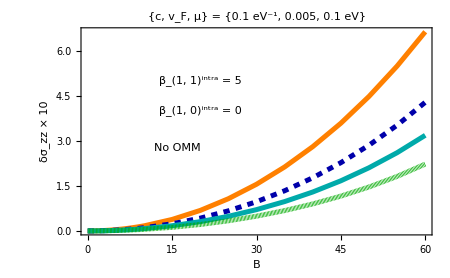

```mathematica
style={(**)Directive[Orange,Thickness[0.008]],(**)Directive[Darker[Blue],Thickness[0.008],Dashing[0.01]],Directive[Darker[Cyan],Thickness[0.008]],(**)Directive[Darker[Green],Thickness[0.008],Dashing[0.001]]};

g1=ListPlot[{dat1,dat2,dat3,dat4},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16,FontFamily->"Times"],PlotRange->{{0,60},All},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,FrameLabel->{"B","δσ_zz × 10"},PlotLabel->Style["{c, v_F, μ} = {0.1 eV^-1, 0.005, 0.1 eV}",Bold,Darker[Brown],18],ImageSize->450,(*****)Epilog->{Style[Text["β_(1, 1)^intra = 5",{20,5}],Darker[Brown],16,Bold],Style[Text["β_(1, 0)^intra = 0",{20,4}],Darker[Brown],16,Bold],(**)Style[Text["No OMM",{16,2.75}],Blue,16,Bold]}(*******)]
```

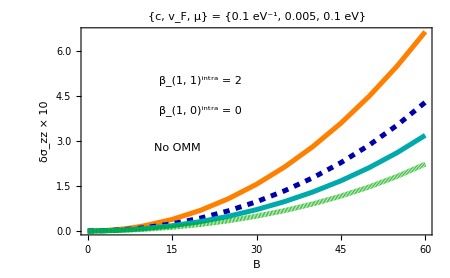

```mathematica
style={(**)Directive[Orange,Thickness[0.008]],(**)Directive[Darker[Blue],Thickness[0.008],Dashing[0.01]],Directive[Darker[Cyan],Thickness[0.008]],(**)Directive[Darker[Green],Thickness[0.008],Dashing[0.001]]};

size=450;
g1=ListPlot[{dat5,dat6,dat7,dat8},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16,FontFamily->"Times"],PlotRange->{{0,60},All},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,FrameLabel->{"B","δσ_zz × 10"},PlotLabel->Style["{c, v_F, μ} = {0.1 eV^-1, 0.005, 0.1 eV}",Bold,Darker[Brown],18],ImageSize->size,(*****)Epilog->{Style[Text["β_(1, 1)^intra = 2",{20,5}],Darker[Brown],16,Bold],Style[Text["β_(1, 0)^intra = 0",{20,4}],Darker[Brown],16,Bold],Style[Text["No OMM",{16,2.75}],Blue,16,Bold]}(*******)]
```

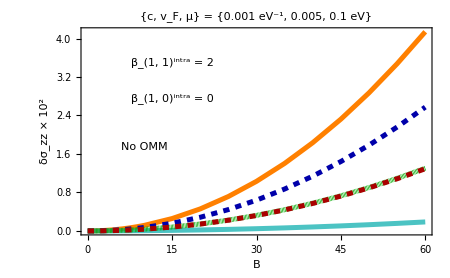

```mathematica
style={(**)Directive[Orange,Thickness[0.008]],(**)Directive[Darker[Blue],Thickness[0.008],Dashing[0.01]],Directive[Darker[Cyan],Thickness[0.008],Opacity[0.7]],(**)Directive[Darker[Green],Thickness[0.008],Dashing[0.001]],Directive[Darker[Red],Thickness[0.008],Dashing[0.01]]};

g1=ListPlot[{dat9,dat10,dat11,dat12,dat13},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16,FontFamily->"Times"],PlotRange->{{0,60},All},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,FrameLabel->{"B","δσ_zz ×  10^2"},PlotLabel->Style["{c, v_F, μ} = {0.001 eV^-1, 0.005, 0.1 eV}",Bold,Darker[Brown],18],ImageSize->450,(*****)Epilog->{Style[Text["β_(1, 1)^intra = 2",{15,3.5}],Darker[Brown],16,Bold],Style[Text["β_(1, 0)^intra = 0",{15,2.75}],Darker[Brown],16,Bold],Style[Text["No OMM",{10,1.75}],Blue,16,Bold]}(*******)]
```